```mathematica
n:={Cos[ϕ],Sin[ϕ],0}/.{ϕ->ϕ[z]}
```

```mathematica
bend:=1/2 K11 Div[n,{x,y,z}]^2//FullSimplify
twist:=1/2 K22(n.Curl[n,{x,y,z}])^2//FullSimplify
splay:=1/2 K33(Cross[n,Curl[n,{x,y,z}]].Cross[n,Curl[n,{x,y,z}]])//Simplify
```

```mathematica
(*elastic energy*)
fgOF=twist+bend+splay/.K33->K11//Simplify
```

1/2 K22 ϕ'[z]^2

```mathematica
1/2 K22 ϕ'[z]^2
```

1/2 K22 ϕ'[z]^2

```mathematica
1/2 K22 ϕ'[z]^2
```

1/2 K22 ϕ'[z]^2

```mathematica
1/2 K22 ϕ'[z]^2
```

1/2 K22 ϕ'[z]^2

```mathematica
1/2 K22 ϕ'[z]^2
```

1/2 K22 ϕ'[z]^2

```mathematica
(*anchoring energy at ϕ[x==xf] is ϕf*)
fgS=-Ws ({Wx,Wy,Wz}.n)^2/.{ϕ[z]->ϕf,Wx->1/Sqrt[2],Wy->1/Sqrt[2],Wz->0}//Simplify
```

-1/2 Ws (1+Sin[2 ϕf])

```mathematica
(*assume the twist is linear (I can prove this but I don't feel like it):*)
ϕlin[z_]:=(ϕf) z/zf
ϕlin[0]
ϕlin[zf]
```

0

ϕf

```mathematica
(*The energy through the bulk is*)
1/2 K22 D[ϕlin[z],z]^2//Simplify
(*Integrated through the bulk, the total energy per unit area is*)
Integrate[%,{z,0,zf}]//Simplify
(*This total energy changes with ϕf, so the bulk applies a torque on ϕf that looks like this:*)
-D[%,ϕf]//Simplify
```

(K22 ϕf^2)/(2 zf^2)

(K22 ϕf^2)/(2 zf)

-(K22 ϕf)/zf

```mathematica
(*The surface energy changes like so with ϕf*)
-D[fgS,ϕf]
```

Ws Cos[2 ϕf]

```mathematica
Ws Cos[2 ϕf]
```

Ws Cos[2 ϕf]

```mathematica
(*The system is at equilibrium when the two torques add to 0. Make a function to find the equilibrium value of ϕf that solves the nonlinear torque balance equation. Notice that there is actually only one variable that matters: the dimensionless ratio Ws*xf/K11 (this should sound familiar). The stuff happens when this thing is around 1. I will leave this function in terms of three variables for clarity though.*)
findequilibriumϕf[Ws_,K22_,zf_]:=ϕf/.FindRoot[(-K22 ( ϕf))/zf+Ws Cos[2 ϕf]==0,{ϕf,1.2}]
```

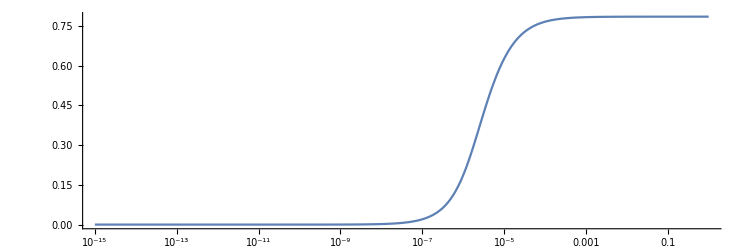

```mathematica
plot1 = Quiet@LogLinearPlot[findequilibriumϕf[Ws,5*^-12,2*^-6],{Ws,10^-15,1},PlotRange->{{10^-15,1},Automatic},AspectRatio->1/3,FrameLabel->(Style[#,SingleLetterItalics->False]&/@{"Ws (J/m^2)","ϕ_f"}),RotateLabel->False,GridLines->{{12/20*10^-6},{π/4,π/2}}]
```

```mathematica
seanData=Import["~/phi4.mat"];
(*seanData=Flatten[MapAt[Log10,seanData,{;;,;;,1}]]*)
seanData = Flatten[Reverse[seanData]]
```

Import::nffil: File not found during Import.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[$Failed].

Reverse[$Failed]

```mathematica
Ws = {1*^-4, 1*^-3, 1*^-2 , .1, 1}
```

{1/10000,1/1000,1/100,0.1,1}

```mathematica
ata ={Ws,seanData}ᵀ
```

Transpose::nmtx: The first two levels of {Ws, Reverse[$Failed]} cannot be transposed.

Transpose[{Ws,Reverse[$Failed]}]

```mathematica
{{-4,1.5653603623426968},{-3,1.5166037514801944},{-2,1.105131987684839},{-1.,0.7853954859638193},{0,0.7853954859638193}}
```

{{-4,1.56536},{-3,1.5166},{-2,1.10513},{-1.,0.785395},{0,0.785395}}

```mathematica
{{-4,1.5653603623426968},{-3,1.5166037514801944},{-2,1.105131987684839},{-1.,0.7853954859638193},{0,0.7853954859638193}}
```

{{-4,1.56536},{-3,1.5166},{-2,1.10513},{-1.,0.785395},{0,0.785395}}

```mathematica
ListLogLinearPlot[ata, PlotRange->Automatic, PlotStyle -> Black, FrameLabel->(Style[#,SingleLetterItalics->False]&/@{"Ws (J/m^2)","ϕ_f"}),RotateLabel->False,GridLines->{{12/20*10^-6},{π/4,π/2}}]
```

ListLogLinearPlot::lpn: Transpose[{Ws, Reverse[$Failed]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogLinearPlot :: lpn will be suppressed during this calculation.

ListLogLinearPlot[Transpose[{Ws,Reverse[$Failed]}],PlotRange→Automatic,PlotStyle→GrayLevel[0],FrameLabel→{Ws (J/m^2),ϕ_f},RotateLabel→False,GridLines→{{3/5000000},{π/4,π/2}}]

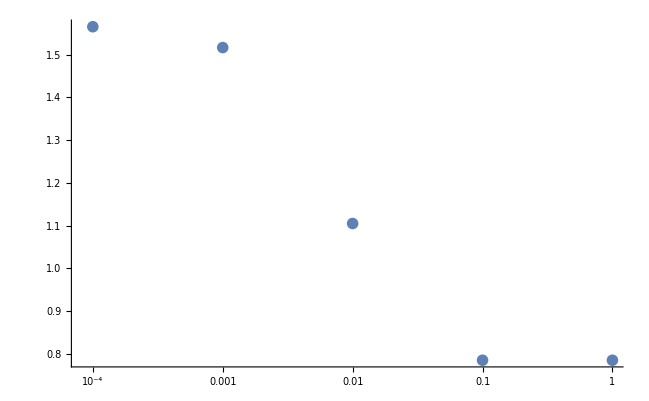

-Graphics-

```mathematica
Show[%943,AxesLabel->{RawBoxes[RowBox[{"Anchoring"," ","Strength","  ",RowBox[{"(",RowBox[{"J","/",RowBox[{"m","^"}]}],")"}]}]],HoldForm[Phi]},FrameLabel->{{None,None},{None,None}},PlotLabel->HoldForm[Anchoring Strength vs Phi],LabelStyle->{FontFamily->"Helvetica",GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%943,AxesLabel→{Anchoring Strength  (J/m^),Phi},FrameLabel→{{None,None},{None,None}},PlotLabel→Anchoring Strength vs Phi,LabelStyle→{FontFamily→Helvetica,GrayLevel[0]}]

```mathematica
Show[%944,PlotLabel->HoldForm[Achoring Strength vs.Phi],LabelStyle->{24,GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%944,PlotLabel→Achoring Strength vs.Phi,LabelStyle→{24,GrayLevel[0]}]

```mathematica
Show[%952,PlotLabel->HoldForm[Anchoring Strength]]
```

Show::gtype: Out is not a type of graphics.

Show[%952,PlotLabel→Anchoring Strength]

```mathematica
Show[%944,ImageSize->Large]
```

Show::gtype: Out is not a type of graphics.

Show[%944,ImageSize→Large]

ListLogPlot::lpn: Transpose[{Ws, Reverse[$Failed]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot :: lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

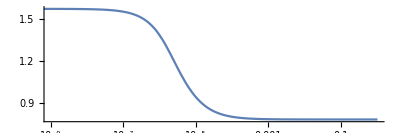
Show[{-Graphics-,ListLogPlot[Transpose[{Ws,Reverse[$Failed]}],PlotStyle→GrayLevel[0]]},PlotRange→{{-9,-1},All},FrameTicks→{MakeTicks[LinTicks[π/4,π/2,π/4,4,TickLabelFunction→(π/<>ToString[Denominator[Rationalize[#1/π]]]&)]],MakeTicks[LogTicks[-11,0]]},PlotRangePadding→Scaled[0.05]]

```mathematica
Show[{plot1,ListLogPlot[ata,PlotStyle->Black]},PlotRange->{{-9,-1},All},FrameTicks->{MakeTicks@LinTicks[π/4,π/2,π/4,4,TickLabelFunction->("π/"<>ToString@Denominator@Rationalize[#/π]&)],MakeTicks@LogTicks[-11,0]},PlotRangePadding->Scaled[.05]]
```

```mathematica
P
```